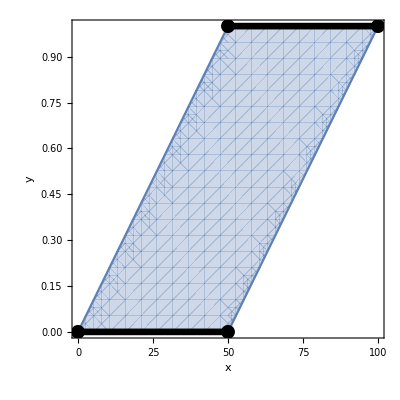

F:\Univ\_PhD\TA\MATH0462\Syllabus\2_3_if-greater-than.pdf

```mathematica
p=RegionPlot[50y≤x&&x≤50(1-y)+100y,{x,0,100},{y,0,1},
FrameLabel->{"x","y"},
Epilog->{
Thickness[.012],
Line[{{0,0},{50,0}}],Line[{{50,1},{100,1}}],
PointSize[.025],
Point[{{0,0},{50,0},{50,1},{100,1}}]
}]
Export[NotebookDirectory[]<>"2_3_if-greater-than.pdf",p]
```